```mathematica
Quit[]
```

## Create test figure

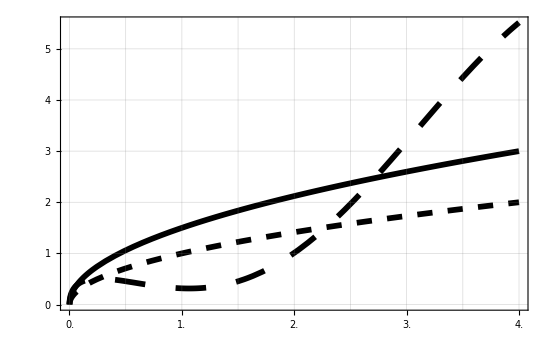

```mathematica
testFig=Plot[{√x,2 √x-2Sin[x],3/2 x^(1/2)},{x,0,4},PlotStyle->{Directive[Dashing[0.02],Black,Thickness[0.0075]],Directive[Dashing[0.04],Black,Thickness[0.0075]],Directive[Black,Thickness[0.0075]]},Frame->True,GridLines->{Range[0,4,0.5],Range[0,5]},GridLinesStyle->Directive[Thick,Opacity[0.3], Gray],FrameTicks->{{Range[0,6,1],None},{Range[0,4,0.5],None}},FrameTicksStyle->Directive[Black,14],ImageSize->550]
```

### Export to pdf file

```mathematica
Export["testFig.pdf",testFig,ImageResolution->720]
```

testFig.pdf

### Snapshot take from pdf, range: 0≤x≤4 and 0≤y≤5 (it’s better to snapshot from the axes origin to some place with a definite tick)

```mathematica
testFig1=-Graphics-;
```

## Extract the points

### Press mouse (prime button) on the figure while holding Shift Key to create a region (the mouse pressing as vertices and their connection as boundary of the polygon-like region) , in which the curves are about to be extracted. The solid line shows the region boundary already selected, the dashed line indicates the boundary waiting to be confirmed by mouse press. Release the Shift Key to end the selection Release the Shift Key and press hold again to clear the region and start new region.

```mathematica
tt=(Unique[x])
```

x$10378

```mathematica
tt=4
```

4

```mathematica
x1
```

x1

```mathematica
Unique["e"]
```

e48

```mathematica
x$10378//Evaluate
```

x$10378

```mathematica
sss={1,3,4}
```

{1,3,4}

```mathematica
?testFig1
```

```mathematica
RgnSlct[imgname_String]:=Block[{bndry={}},"DynamicModule[{p={}},
EventHandler[Dynamic@Show["<>imgname<>",Graphics[{Blue,Line["<>"bndry"<>"]}],Graphics[{Blue,Dashed,If[Length[p]>0,Line[{Last[p],Dynamic[MousePosition[\"Graphics\"]]}]]}],ImageSize→600],{If[CurrentValue[\"ShiftKey\"],\"MouseDown\":>(AppendTo[p,MousePosition[\"Graphics\"]];"<>"bndry"<>"=p)]}]]//Dynamic"]
```

```mathematica
f[imgname_String,bndry_String]:=ToExpression[bndry<>"={};DynamicModule[{p={}},
EventHandler[Dynamic@Show["<>imgname<>",Graphics[{Blue,Line["<>bndry<>"]}],Graphics[{Blue,Dashed,If[Length[p]>0,Line[{Last[p],Dynamic[MousePosition[\"Graphics\"]]}]]}],ImageSize→600],{If[CurrentValue[\"ShiftKey\"],\"MouseDown\":>(AppendTo[p,MousePosition[\"Graphics\"]];"<>bndry<>"=p)]}]]//Dynamic"]
```

```mathematica
f["testFig1","coords"]
```

### Binarize the fig and select the points within the above region

```mathematica
f1f[x_]:=x^2
```

```mathematica
f1f//Head
```

Symbol

```mathematica
DataExtrct[imgname_String,bndry_,RsclF_,thrshld_:0.5,lngthcut_:0]:=Module[{Rgn,PntsPstn,pxcl},Rgn=BoundaryDiscretizeRegion[Polygon[bndry]];PntsPstn=Position[Transpose[ImageData[Binarize[ToExpression[imgname],thrshld],DataReversed->True]],0];pxcl=Mean/@DeleteCases[GatherBy[Select[PntsPstn,#∈Rgn&],#⟦1⟧&],_?(Length[#]<lngthcut&)];RsclF&/@pxcl]
```

```mathematica
DataExtrct[]
```

```mathematica
Quit[]
```

```mathematica
<<PointExtract`
```

```mathematica
InFgBnrzd=ImageData[Binarize[testFig1,0.5],DataReversed->True]//Transpose;
```

```mathematica
PntsPstn=Position[InFgBnrzd,0];
```

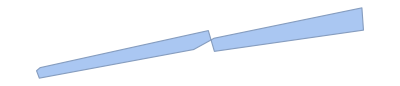

```mathematica
Rgn=BoundaryDiscretizeRegion[Polygon[coords]]
```

### Take mean value of points with the same x-value (due to the width of curves) and rescale the points to data set

```mathematica
PntsExtrctd=Mean/@DeleteCases[GatherBy[Select[PntsPstn,#∈Rgn&],#⟦1⟧&],_?(Length[#]<10&)];
```

```mathematica
PntsExtrctdRscld=({4#⟦1⟧,5#⟦2⟧}/ImageDimensions[InFg])&/@PntsExtrctd;
```

## Compare extraction and original curve

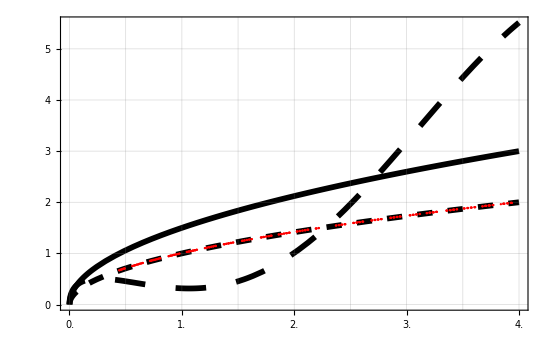

```mathematica
Show[{testFig,ListPlot[PntsExtrctdRscld,PlotStyle->{Red,PointSize[0.003]}]}]
```

```mathematica
PntsExtrctdRscld//N//InputForm
```

{{0.4424934152765584, 0.6708333333333333}, {0.44600526777875327, 0.6708333333333333}, {0.45302897278314314, 0.6791666666666667}, 
 {0.456540825285338, 0.6791666666666667}, {0.4635645302897278, 0.6875}, {0.46707638279192276, 0.6875}, {0.4741000877963126, 0.6958333333333333}, 
 {0.47761194029850745, 0.6958333333333333}, {0.48463564530289727, 0.7041666666666667}, {0.4881474978050922, 0.7041666666666667}, 
 {0.4916593503072871, 0.7041666666666667}, {0.5583845478489904, 0.7541666666666667}, {0.5618964003511853, 0.7541666666666667}, 
 {0.57243195785777, 0.7625}, {0.5759438103599649, 0.7625}, {0.5829675153643546, 0.7708333333333334}, {0.5864793678665496, 0.7708333333333334}, 
 {0.5970149253731343, 0.7791666666666667}, {0.6005267778753293, 0.7791666666666667}, {0.611062335381914, 0.7875}, {0.6145741878841089, 0.7875}, 
 {0.6215978928884986, 0.7958333333333333}, {0.6251097453906936, 0.7958333333333333}, {0.6356453028972783, 0.8041666666666667}, 
 {0.6391571553994733, 0.8041666666666667}, {0.6496927129060579, 0.8125}, {0.6532045654082529, 0.8125}, {0.7164179104477612, 0.8541666666666666}, 
 {0.7199297629499561, 0.8541666666666666}, {0.723441615452151, 0.8541666666666666}, {0.7304653204565408, 0.8625}, {0.7339771729587358, 0.8625}, 
 {0.7445127304653204, 0.8708333333333333}, {0.7480245829675154, 0.8708333333333333}, {0.7515364354697103, 0.8708333333333333}, 
 {0.762071992976295, 0.8791666666666667}, {0.7655838454784899, 0.8791666666666667}, {0.7761194029850746, 0.8875}, {0.7796312554872695, 0.8875}, 
 {0.7901668129938543, 0.8958333333333334}, {0.7936786654960492, 0.8958333333333334}, {0.8042142230026339, 0.9041666666666667}, 
 {0.8077260755048288, 0.9041666666666667}, {0.8814749780509219, 0.9458333333333333}, {0.8849868305531168, 0.9458333333333333}, 
 {0.8955223880597015, 0.9541666666666667}, {0.8990342405618964, 0.9541666666666667}, {0.9025460930640913, 0.9541666666666667}, 
 {0.913081650570676, 0.9625}, {0.9165935030728709, 0.9625}, {0.9271290605794557, 0.9708333333333333}, {0.9306409130816505, 0.9708333333333333}, 
 {0.9341527655838455, 0.9708333333333333}, {0.9446883230904302, 0.9791666666666666}, {0.9482001755926251, 0.9791666666666666}, 
 {0.9622475856014048, 0.9875}, {0.9657594381035997, 0.9875}, {0.9762949956101844, 0.9958333333333333}, {0.9798068481123793, 0.9958333333333333}, 
 {1.0430201931518877, 1.0291666666666666}, {1.0465320456540825, 1.0291666666666666}, {1.0500438981562774, 1.0291666666666666}, 
 {1.0605794556628623, 1.0375}, {1.0640913081650571, 1.0375}, {1.067603160667252, 1.0375}, {1.0781387181738367, 1.0458333333333334}, 
 {1.0816505706760315, 1.0458333333333334}, {1.0851624231782264, 1.0458333333333334}, {1.0956979806848113, 1.0541666666666667}, 
 {1.0992098331870062, 1.0541666666666667}, {1.102721685689201, 1.0541666666666667}, {1.1132572431957857, 1.0625}, {1.1167690956979808, 1.0625}, 
 {1.1202809482001757, 1.0625}, {1.1308165057067603, 1.0708333333333333}, {1.1343283582089552, 1.0708333333333333}, 
 {1.2045654082528534, 1.1041666666666667}, {1.2080772607550483, 1.1041666666666667}, {1.222124670763828, 1.1125}, {1.225636523266023, 1.1125}, 
 {1.2396839332748024, 1.1208333333333333}, {1.2431957857769973, 1.1208333333333333}, {1.2467076382791922, 1.1208333333333333}, 
 {1.260755048287972, 1.1291666666666667}, {1.2642669007901668, 1.1291666666666667}, {1.2783143107989465, 1.1375}, {1.2818261633011414, 1.1375}, 
 {1.295873573309921, 1.1458333333333333}, {1.2993854258121158, 1.1458333333333333}, {1.302897278314311, 1.1458333333333333}, 
 {1.373134328358209, 1.1791666666666667}, {1.3766461808604038, 1.1791666666666667}, {1.3801580333625987, 1.1791666666666667}, 
 {1.3942054433713784, 1.1875}, {1.3977172958735733, 1.1875}, {1.411764705882353, 1.1958333333333333}, {1.415276558384548, 1.1958333333333333}, 
 {1.4187884108867428, 1.1958333333333333}, {1.4328358208955223, 1.2041666666666666}, {1.4363476733977174, 1.2041666666666666}, 
 {1.4398595258999123, 1.2041666666666666}, {1.4539069359086918, 1.2125}, {1.4574187884108867, 1.2125}, {1.5346795434591747, 1.2458333333333333}, 
 {1.5381913959613696, 1.2458333333333333}, {1.5417032484635644, 1.2458333333333333}, {1.5557506584723442, 1.2541666666666667}, 
 {1.559262510974539, 1.2541666666666667}, {1.5768217734855137, 1.2625}, {1.5803336259877085, 1.2625}, {1.5978928884986832, 1.2708333333333333}, 
 {1.601404741000878, 1.2708333333333333}, {1.6189640035118524, 1.2791666666666666}, {1.6224758560140473, 1.2791666666666666}, 
 {1.7032484635645302, 1.3125}, {1.7067603160667253, 1.3125}, {1.7102721685689202, 1.3125}, {1.7243195785776997, 1.3208333333333333}, 
 {1.7278314310798946, 1.3208333333333333}, {1.7313432835820894, 1.3208333333333333}, {1.748902546093064, 1.3291666666666666}, 
 {1.752414398595259, 1.3291666666666666}, {1.7699736611062336, 1.3375}, {1.7734855136084284, 1.3375}, {1.7769973661106233, 1.3375}, 
 {1.791044776119403, 1.3458333333333334}, {1.794556628621598, 1.3458333333333334}, {1.7980684811237928, 1.3458333333333334}, 
 {1.861281826163301, 1.3708333333333333}, {1.864793678665496, 1.3708333333333333}, {1.8823529411764706, 1.3791666666666667}, 
 {1.8858647936786654, 1.3791666666666667}, {1.8893766461808603, 1.3791666666666667}, {1.906935908691835, 1.3875}, {1.9104477611940298, 1.3875}, 
 {1.9280070237050044, 1.3958333333333333}, {1.9315188762071993, 1.3958333333333333}, {1.9350307287093942, 1.3958333333333333}, 
 {1.9525899912203688, 1.4041666666666666}, {1.9561018437225637, 1.4041666666666666}, {1.9596136962247586, 1.4041666666666666}, 
 {2.022827041264267, 1.4291666666666667}, {2.0263388937664617, 1.4291666666666667}, {2.029850746268657, 1.4291666666666667}, 
 {2.0474100087796314, 1.4375}, {2.050921861281826, 1.4375}, {2.054433713784021, 1.4375}, {2.071992976294996, 1.4458333333333333}, 
 {2.0755048287971904, 1.4458333333333333}, {2.093064091308165, 1.4541666666666666}, {2.09657594381036, 1.4541666666666666}, 
 {2.100087796312555, 1.4541666666666666}, {2.1176470588235294, 1.4625}, {2.1211589113257245, 1.4625}, {2.124670763827919, 1.4625}, 
 {2.1913959613696226, 1.4875}, {2.194907813871817, 1.4875}, {2.1984196663740123, 1.4875}, {2.215978928884987, 1.4958333333333333}, 
 {2.2194907813871816, 1.4958333333333333}, {2.370500438981563, 1.5458333333333334}, {2.3740122914837576, 1.5458333333333334}, 
 {2.3950834064969273, 1.5541666666666667}, {2.398595258999122, 1.5541666666666667}, {2.402107111501317, 1.5541666666666667}, 
 {2.4196663740122917, 1.5625}, {2.4231782265144863, 1.5625}, {2.4266900790166814, 1.5625}, {2.4477611940298507, 1.5708333333333333}, 
 {2.451273046532046, 1.5708333333333333}, {2.4547848990342405, 1.5708333333333333}, {2.525021949078139, 1.5958333333333334}, 
 {2.5285338015803336, 1.5958333333333334}, {2.5320456540825287, 1.5958333333333334}, {2.553116769095698, 1.6041666666666667}, 
 {2.556628621597893, 1.6041666666666667}, {2.5601404741000877, 1.6041666666666667}, {2.5776997366110623, 1.6125}, {2.5812115891132574, 1.6125}, 
 {2.584723441615452, 1.6125}, {2.605794556628622, 1.6208333333333333}, {2.6093064091308165, 1.6208333333333333}, 
 {2.6128182616330116, 1.6208333333333333}, {2.6865671641791047, 1.6458333333333333}, {2.6900790166812993, 1.6458333333333333}, 
 {2.6935908691834944, 1.6458333333333333}, {2.7146619841966637, 1.6541666666666666}, {2.718173836698859, 1.6541666666666666}, 
 {2.7216856892010535, 1.6541666666666666}, {2.742756804214223, 1.6625}, {2.746268656716418, 1.6625}, {2.749780509218613, 1.6625}, 
 {2.770851624231782, 1.6708333333333334}, {2.7743634767339773, 1.6708333333333334}, {2.777875329236172, 1.6708333333333334}, 
 {2.85513608428446, 1.6958333333333333}, {2.858647936786655, 1.6958333333333333}, {2.86215978928885, 1.6958333333333333}, 
 {2.8832309043020192, 1.7041666666666666}, {2.8867427568042143, 1.7041666666666666}, {2.890254609306409, 1.7041666666666666}, 
 {2.9113257243195787, 1.7125}, {2.9148375768217734, 1.7125}, {2.9183494293239685, 1.7125}, {2.9394205443371377, 1.7208333333333334}, 
 {2.942932396839333, 1.7208333333333334}, {2.9464442493415275, 1.7208333333333334}, {3.0272168568920104, 1.7458333333333333}, 
 {3.0307287093942055, 1.7458333333333333}, {3.0342405618964006, 1.7458333333333333}, {3.05531167690957, 1.7541666666666667}, 
 {3.0588235294117645, 1.7541666666666667}, {3.0623353819139596, 1.7541666666666667}, {3.083406496927129, 1.7625}, {3.086918349429324, 1.7625}, 
 {3.090430201931519, 1.7625}, {3.1150131694468834, 1.7708333333333333}, {3.118525021949078, 1.7708333333333333}, {3.1782265144863917, 1.7875}, 
 {3.1817383669885864, 1.7875}, {3.202809482001756, 1.7958333333333334}, {3.2063213345039507, 1.7958333333333334}, 
 {3.209833187006146, 1.7958333333333334}, {3.230904302019315, 1.8041666666666667}, {3.23441615452151, 1.8041666666666667}, 
 {3.237928007023705, 1.8041666666666667}, {3.2414398595259, 1.8041666666666667}, {3.2625109745390692, 1.8125}, {3.2660228270412643, 1.8125}, 
 {3.269534679543459, 1.8125}, {3.353819139596137, 1.8375}, {3.357330992098332, 1.8375}, {3.3608428446005267, 1.8375}, 
 {3.385425812115891, 1.8458333333333334}, {3.388937664618086, 1.8458333333333334}, {3.392449517120281, 1.8458333333333334}, 
 {3.4135206321334506, 1.8541666666666667}, {3.4170324846356452, 1.8541666666666667}, {3.4205443371378403, 1.8541666666666667}, 
 {3.424056189640035, 1.8541666666666667}, {3.4451273046532047, 1.8625}, {3.4486391571553994, 1.8625}, {3.508340649692713, 1.8791666666666667}, 
 {3.5118525021949076, 1.8791666666666667}, {3.5153643546971027, 1.8791666666666667}, {3.539947322212467, 1.8875}, {3.5434591747146618, 1.8875}, 
 {3.546971027216857, 1.8875}, {3.5715539947322212, 1.8958333333333333}, {3.5750658472344163, 1.8958333333333333}, 
 {3.578577699736611, 1.8958333333333333}, {3.6031606672519754, 1.9041666666666666}, {3.6066725197541705, 1.9041666666666666}, 
 {3.610184372256365, 1.9041666666666666}, {3.6733977172958734, 1.9208333333333334}, {3.6769095697980685, 1.9208333333333334}, 
 {3.6979806848112378, 1.9291666666666667}, {3.701492537313433, 1.9291666666666667}, {3.705004389815628, 1.9291666666666667}, 
 {3.7085162423178226, 1.9291666666666667}, {3.729587357330992, 1.9375}, {3.733099209833187, 1.9375}, {3.736611062335382, 1.9375}, 
 {3.7401229148375768, 1.9375}, {3.764705882352941, 1.9458333333333333}, {3.7682177348551362, 1.9458333333333333}, 
 {3.771729587357331, 1.9458333333333333}, {3.8384547848990342, 1.9625}, {3.8595258999122035, 1.9708333333333334}, 
 {3.8630377524143986, 1.9708333333333334}, {3.8665496049165937, 1.9708333333333334}, {3.8700614574187884, 1.9708333333333334}, 
 {3.8946444249341527, 1.9791666666666667}, {3.898156277436348, 1.9791666666666667}, {3.9016681299385425, 1.9791666666666667}, 
 {3.926251097453907, 1.9875}, {3.929762949956102, 1.9875}, {3.9332748024582966, 1.9875}, {3.9367866549604917, 1.9875}}